```mathematica
<<InitPackages`
DateString[]
```

Fri 5 Aug 2011 22:20:23

## Calculation of π Using a Numerical Integraltion

```mathematica
MPAFE[HoldForm@∫_0^1 4/(1+x^2)ⅆx,MPEvaluateInt,All]
```

∫_0^1 4/(1+x^2)ⅆx==π

## Standard Normal Distribution

```mathematica
Subscript[φ, μ,σ^2][x]==1/(σ √(2π))ⅇ^((-(x-μ)^2)/(2 σ^2))
MPMAF[%,MPEliminate,{At[2],{μ==0,σ^2==1},{μ,σ}}]
```

φ_(μ,σ^2)[x]==(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

φ_(μ,σ^2)[x]==(ⅇ^(-x^2/2))/(√(2 π))

φ_(μ,σ^2)[x]==(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))

{0.892062 ⅇ^(-2.5 x^2),0.398942 ⅇ^(-0.5 x^2),0.178412 ⅇ^(-0.1 x^2),0.56419 ⅇ^(-1. (2+x)^2)}

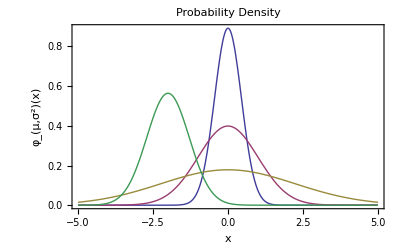

```mathematica
Subscript[φ, μ,σ^2][x]==1/(√(2π σ^2))ⅇ^((-(x-μ)^2)/(2 σ^2))
%[[2]]//{Tooltip[#/.{μ->0,σ^2->0.2,σ^-2->0.2^-1},"μ==0,σ^2==0.2"],Tooltip[#/.{μ->0,σ^2->1.0,σ^-2->1.0^-1},"μ==0,σ^2==1.0"],Tooltip[#/.{μ->0,σ^2->5.0,σ^-2->5.0^-1},"μ==0,σ^2==5.0"],Tooltip[#/.{μ->-2,σ^2->0.5,σ^-2->0.5^-1},"μ==-2,σ^2==0.5"]}&
Plot[%,{x,-5,5},Axes->False,Frame->True,PlotRange->All,FrameLabel->{x,Subscript[φ, μ,σ^2][x]},PlotLabel->"Probability Density"]
```

```mathematica
Subscript[Ψ, μ,σ^2][z]==1/(√(2π σ^2))HoldForm@∫_(-∞)^z ⅇ^((-(x-μ)^2)/(2 σ^2))ⅆx
MPMAF[%,MPEvalInt,At[2],
Refine,{All,σ>0}]
```

Ψ_(μ,σ^2)[z]==1/(√(2 π) √(σ^2)) ∫_(-∞)^z ⅇ^(-(x-μ)^2/(2 σ^2))ⅆx

ConditionalExpression[Ψ_(μ,σ^2)[z]==σ/(2 √(σ^2)) (√(1/σ^2) σ+Erf[(z-μ)/(√2 σ)]),Re[σ^2]>0]

Ψ_(μ,σ^2)[z]==1/2 (1+Erf[(z-μ)/(√2 σ)])

Ψ_(μ,σ^2)[z]==1/2 (1+Erf[(z-μ)/(√2 σ)])

Ψ_(μ,σ^2)[z]==1/2 (1+Erf[(z-μ)/(√2 √(σ^2))])

{1/2 (1+Erf[1.58114 z]),1/2 (1+Erf[0.707107 z]),1/2 (1+Erf[0.316228 z]),1/2 (1+Erf[1. (2+z)])}

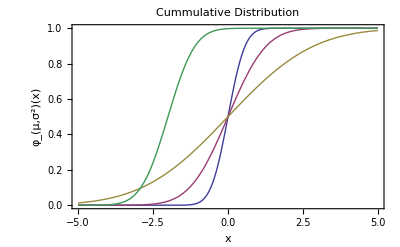

```mathematica
Subscript[Ψ, μ,σ^2][z]==1/2 (1+Erf[(z-μ)/(√2 σ)])
MPMAF[%,ReplaceAll,{At[2],σ->√(σ^2)}]
%[[2]]//{Tooltip[#/.{μ->0,σ^2->0.2},"μ==0,σ^2==0.2"],Tooltip[#/.{μ->0,σ^2->1.0},"μ==0,σ^2==1.0"],Tooltip[#/.{μ->0,σ^2->5.0},"μ==0,σ^2==5.0"],Tooltip[#/.{μ->-2,σ^2->0.5},"μ==-2,σ^2==0.5"]}&
Plot[%,{z,-5,5},Axes->False,Frame->True,PlotRange->All,FrameLabel->{x,Subscript[φ, μ,σ^2][x]},PlotLabel->"Cummulative Distribution"]
```